```mathematica
β=0.2;
μ=0.05;
eq={
s'[t]==-β s[t]i[t],
i'[t]==β i[t]s[t]-μ i[t],
r'[t]==μ i[t],
r[0]==0,
i[0]==0.01,
s[0]==1-r[0]-i[0]
};
solution=NDSolve[eq,{i,r,s},{t,0,150}];
```

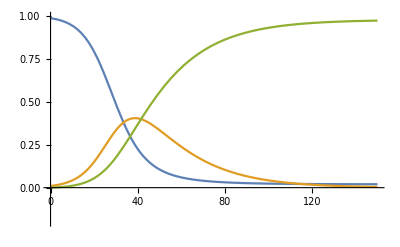

```mathematica
s1=First[s/.solution];
i1=First[i/.solution];
r1=First[r/.solution];

Plot[{s1[t],i1[t],r1[t]},{t,0,150},PlotRange->{-0.2, 1}]
```

```mathematica
eqFirst:={
y'[x]==(x y[x]^2+x y[x])/(9-x^2),
y[0]==0.05
};
intFirst={x,0,2.5};
eqSecond:={
y'[x]==(2x y[x])/(3 x^2-y[x]^2),
y[1]==1
};
intSecond={x,1,3};
```

```mathematica
firstSolve=NDSolve[eqFirst,y,intFirst];
secondSolve=NDSolve[eqSecond,y,intSecond];
```

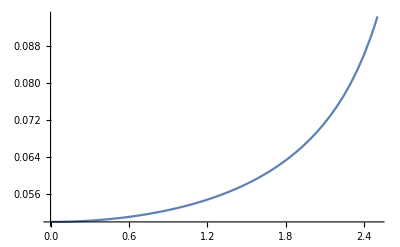

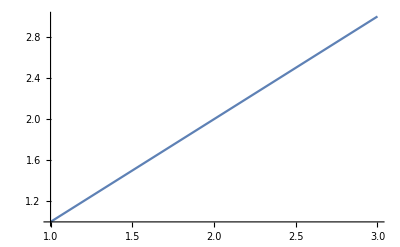

```mathematica
firstGraph=First[y/.firstSolve];
secondGraph=First[y/.secondSolve];
Plot[firstGraph[x],intFirst]
Plot[secondGraph[x],intSecond]
```

## Runge-Kutta classic method

```mathematica
a={0,1./2.,1./2.,1};
λ={1./6.,2./6.,2./6.,1./6.};
b={
{1./2.,0,0},
{0,1./2.,0},
{0,0,1}
};
τ=10^-0;
```

```mathematica
k[func_,t_,y_,i_]:=func[t+a[[i]]τ,y+Sum[b[[i-1]][[j]]τ k[func,t,y,i-1],{j,1,i-1}]];

kVec[func_,t_,y_,i_]:=Module[{},
Return[Table[func[[ind]][t+a[[i]]τ,y+Sum[b[[i-1]][[j]]τ kVec[func,t,y,i-1],{j,1,i-1}]],{ind, 1, Length[func]}]
];
];

RungeKutta[func_,x0_,y0_]:=Module[{y={},currY=y0,currX=x0},
While[currX<2.5,
currY=currY+τ Sum[λ[[i]]k[func,currX,currY,i],{i,1,4}];
currX+=τ;
y=Append[y,currX];
];
Return[y];
]
RungeKuttaVec[func_,x0_,y0_]:=Module[{y={y0},currY=y0,currX=x0},
While[currX<100,
currY=currY+τ Sum[λ[[i]]kVec[func,currX,currY,i],{i,1,4}];
currX+=τ;
y=Append[y,currY];
];
Return[y];
]
```

```mathematica
f[x_,y_]:=(x y^2+x y)/(9-x^2);
res=RungeKutta[f,0.,0.05];
```

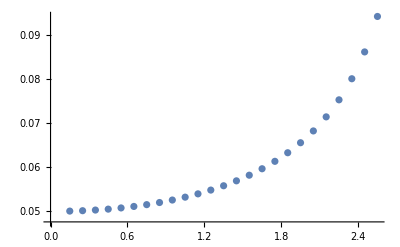

```mathematica
ListPlot[{Table[{0.05+τ i,res[[i]]},{i,0,2.5/τ}]}]
```

```mathematica
modelS[x_,yV_]:=-β yV[[1]] yV[[2]];
modelI[x_,yV_]:=β yV[[2]] yV[[1]]-μ yV[[2]];
modelR[x_,yV_]:=μ yV[[2]];

res=RungeKuttaVec[{modelS,modelI,modelR},0,{0.99,0.01,0}];
```

```mathematica
res
```

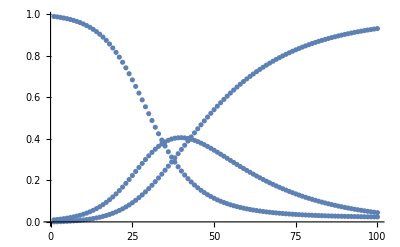

```mathematica
Show[
ListPlot[{Table[{0.05+τ i,res[[i]][[1]]},{i,1,100/τ}]}],
ListPlot[{Table[{0.05+τ i,res[[i]][[2]]},{i,1,100/τ}]}],
ListPlot[{Table[{0.05+τ i,res[[i]][[3]]},{i,1,100/τ}]}]
]
```